{-(ⅇ^(-(-2+x)^2/(2 σ^2)) (-2+x))/(√(2 π) σ^3)}

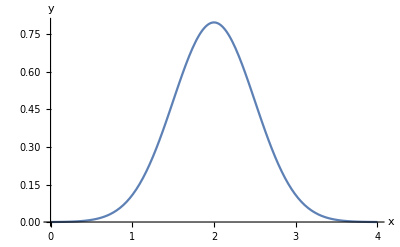

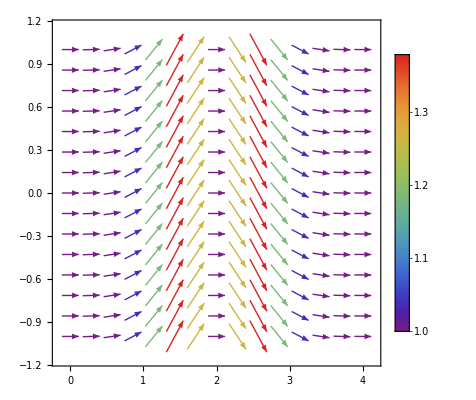

```mathematica
G1[x_,σ_]:=(1/((σ)*Sqrt[2Pi]))Exp[-((x-a)^2)/(2σ^2)];
a=2;
grad[x_,σ_]=Grad[G1[x,σ],{x}]
Plot[G1[x,σ=0.5], {x, 0,4},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"}]
VectorPlot[{1,grad[x,σ=0.5]},{x,0,4},{y,-1,1},VectorStyle->Black,VectorColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
Exit
```

```mathematica
G2[x_,y_,σ_]:=(1/((σ^2)*2Pi))Exp[-(((x-a)^2)+((y-b)^2))/(2σ^2)];
a=2;b=2;
grad[x_,y_,σ_]=Grad[G2[x,y,σ],{x,y}]
Plot3D[G2[x,y,σ=0.5], {x, 0,4},{y,0,4},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
plot1=ContourPlot[G2[x,y,σ=0.5], {x, 0,4},{y,0,4},PlotPoints->100,Contours->30,ContourStyle->Gray,PlotLegends->Automatic,ColorFunction->"Rainbow"];
plot2=VectorPlot[grad[x,y,σ=0.5],{x,0,4},{y,0,4},VectorStyle->Black];
Show[plot1,plot2]
```

{-(ⅇ^((-(-2+x)^2-(-2+y)^2)/(2 σ^2)) (-2+x))/(2 π σ^4),-(ⅇ^((-(-2+x)^2-(-2+y)^2)/(2 σ^2)) (-2+y))/(2 π σ^4)}

-Graphics3D-

-Graphics-

```mathematica
g2[x_,y_]:=Exp[-x^2]+Exp[-y^2];
grad[x_,y_]=Grad[g2[x,y],{x,y}]
Plot3D[g2[x,y], {x, -5,5},{y,-5,5},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
plot1=ContourPlot[g2[x,y], {x, -5,5},{y,-5,5},PlotPoints->100,Contours->30,ContourStyle->Gray,PlotLegends->Automatic,ColorFunction->"Rainbow"];
plot2=VectorPlot[grad[x,y],{x,-5,5},{y,-5,5},VectorStyle->Black];
Show[plot1,plot2]
```

{-2 ⅇ^(-x^2) x,-2 ⅇ^(-y^2) y}

-Graphics3D-

-Graphics-

```mathematica
f[x_,y_]:=-((Cos[x])^2+(Cos[y])^2)^2;
grad[x_,y_]=Grad[f[x,y],{x,y}]
Plot3D[f[x,y],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},Mesh->None,AxesLabel->{"x","y"}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow",AxesLabel->{"x","y"}];
plot2=VectorPlot[grad[x,y],{x,-2,2},{y,-2,2},VectorStyle->Black,FrameLabel->{"x","y"}];
Show[plot1,plot2]
```

{4 Cos[x] (Cos[x]^2+Cos[y]^2) Sin[x],4 Cos[y] (Cos[x]^2+Cos[y]^2) Sin[y]}

-Graphics3D-

-Graphics-

```mathematica
Directory[]
```

C:\Users\SAMPAD\OneDrive\Documents

```mathematica
SetDirectory[]
```